```mathematica
cols=Short[ColorData[109,"ColorList"],4];
col1=cols[[1,8]]
col2=cols⟦1,9⟧
col3=cols[[1,10]]
col4=cols[[1,7]]
col5=cols⟦1,5⟧
col6=cols⟦1,14⟧
```

RGBColor[1., 0.325204, 0.406504]

RGBColor[0., 0.786874, 0.739379]

RGBColor[1., 0.520437, 0.]

RGBColor[0.238758, 0.610466, 1.]

RGBColor[0.893126, 0.4, 0.767184]

RGBColor[0, 0.7226017980018511, 0.9321946059944466]

```mathematica
δ[p_,q_]:=Subscript[δ, min]+(Subscript[δ, 0]-Subscript[δ, min])*Exp[-(p-q)^2/(2*Subscript[k, 1]^2)];
ρ[p_]:=Subscript[ρ, min]+(Subscript[ρ, 0]-Subscript[ρ, min])*Exp[-p^2/(2*Subscript[k, 2]^2)];
μ[q_]:=Subscript[μ, min]+(Subscript[μ, 0]-Subscript[μ, min])*Exp[-q^2/(2*Subscript[k, 3]^2)];
G1[ϕ1_,p_,q1_,q2_,u_,v1_,v2_]:=ρ[ϕ1]*(1-u/κ)*(u/τ-1)-(δ[ϕ1,q1]*v1)/(1+δ[ϕ1,q1]*γ*u)-(δ[ϕ1,q2]*v2)/(1+δ[ϕ1,q2]*γ*u);
G21[ϕ21_,p_,q1_,q2_,u_,v1_,v2_]:=(α*δ[p,ϕ21]*u)/(1+δ[p,ϕ21]*γ*u)-μ[ϕ21];
G22[ϕ22_,p_,q1_,q2_,u_,v1_,v2_]:=(α*δ[p,ϕ22]*u)/(1+δ[p,ϕ22]*γ*u)-μ[ϕ22];
G11[p_,q1_,q2_,u_,v1_,v2_]:=D[G1[ϕ1,p,q1,q2,u,v1,v2],{ϕ1,1} ] /.ϕ1->p;
G212[p_,q1_,q2_,u_,v1_,v2_]:=D[G21[ϕ21,p,q1,q2,u,v1,v2],{ϕ21,1} ] /.ϕ21->q1;
G222[p_,q1_,q2_,u_,v1_,v2_]:=D[G22[ϕ22,p,q1,q2,u,v1,v2],{ϕ22,1} ] /.ϕ22->q2;
```

```mathematica
Subscript[ρ, 0]=0.75;Subscript[ρ, min]=0.25;κ=35;Subscript[δ, 0]=0.15;Subscript[δ, min]=0.05;γ=0.1;α=0.7;Subscript[μ, 0]=2.0;Subscript[μ, min]=1.0;Subscript[k, 1]=1.0;Subscript[k, 2]=1.0;Subscript[k, 3]=1.0;f=0.5;
τ=1;
sol2=NDSolve[{u'[t]==u[t]*G1[p[t],p[t],q1[t],q2[t],u[t],v1[t],v2[t]],p'[t]==f*G11[p[t],q1[t],q2[t],u[t],v1[t],v2[t]],v1'[t]==v1[t]*G21[q1[t],p[t],q1[t],q2[t],u[t],v1[t],v2[t]],q1'[t]==f*G212[p[t],q1[t],q2[t],u[t],v1[t],v2[t]],v2'[t]==v2[t]*G22[q2[t],p[t],q1[t],q2[t],u[t],v1[t],v2[t]],q2'[t]==f*G222[p[t],q1[t],q2[t],u[t],v1[t],v2[t]],u[0]==3,p[0]==2,v1[0]==3,q1[0]==-2,v2[0]==3,q2[0]==-2.1},{u,p, v1,q1,v2,q2},{t,0,20000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];
```

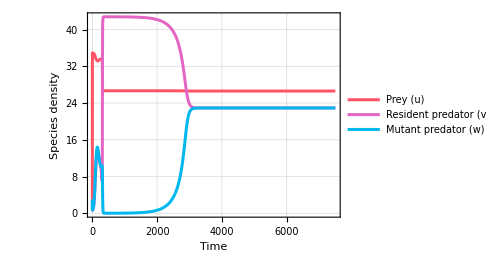

```mathematica
B1=Plot[Evaluate[{u[t],v1[t],v2[t]}/. sol2],{t,0,7500},PlotRange->{All,All},PlotLegends->Placed[{"Prey (u)","Resident predator (v)","Mutant predator (w)"},{0.68,0.24}],LabelStyle->{FontSize->16},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Time","Species density"},PlotStyle->{{col1,Thickness[0.006]},{col5,Thickness[0.006]},{col6,Thickness[0.006]}},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.5],Dotted,Thickness[0.002]],AspectRatio->1.5/2.1,ImageSize->Medium]
```

```mathematica
G111[t_,ϕ_]:=G1[ϕ,p[t]/. sol2[[1]],q1[t]/. sol2[[1]],q2[t]/. sol2[[1]],u[t]/. sol2[[1]],v1[t]/. sol2[[1]],v2[t]/. sol2[[1]]];
G222[t_,ϕ_]:=G21[ϕ,p[t]/. sol2[[1]],q1[t]/. sol2[[1]],q2[t]/. sol2[[1]],u[t]/. sol2[[1]],v1[t]/. sol2[[1]],v2[t]/. sol2[[1]]];
(*-----------------------------fig 4C-------------------------------*)
j1=Plot3D[G111[t,ϕ],{ϕ,-4,4},{t,0,4000},PlotRange->{{-4,4},{0,4000},{-2,1}},Mesh->{4,4},MeshStyle->{White,White},Boxed->False,BoundaryStyle->None,Axes->True,AxesStyle->Directive[Black,Thickness[0.003]],AxesLabel->{"Evolutionary strategy","Time","Fitness"},LabelStyle->Directive[Black,16],BoxRatios->{1,1,1},PlotStyle->{col5,Opacity[0.6]},(*PlotPoints->500,*)ClippingStyle->None,(*PlotLabel->Style["B",20],*)ImageSize->450];

(*-----------------------------fig 4D-------------------------------*)
j2=Plot3D[G222[t,ϕ],{ϕ,-6,6},{t,0,4000},PlotRange->{{-6,6},{0,4000},{-2,1}},Mesh->{4,4},MeshStyle->{Black,Black},Boxed->False,BoundaryStyle->None,PlotStyle->{col6, Opacity[0.6]}(*,PlotPoints->50*)];

(*------------------solution on landscapes-----------------------------*)
G1111[t_]:=G1[p[t]/. sol2[[1]],p[t]/. sol2[[1]],q1[t]/. sol2[[1]],q2[t]/. sol2[[1]],u[t]/. sol2[[1]],v1[t]/. sol2[[1]],v2[t]/. sol2[[1]]];
G2122[t_]:=G21[q1[t]/. sol2[[1]],p[t]/. sol2[[1]],q1[t]/. sol2[[1]],q2[t]/. sol2[[1]],u[t]/. sol2[[1]],v1[t]/. sol2[[1]],v2[t]/. sol2[[1]]];
G2222[t_]:=G22[q2[t]/. sol2[[1]],p[t]/. sol2[[1]],q1[t]/. sol2[[1]],q2[t]/. sol2[[1]],u[t]/. sol2[[1]],v1[t]/. sol2[[1]],v2[t]/. sol2[[1]]];

(*-----------------strategy on landscape prey--------------------*)
k1=ParametricPlot3D[{p[t]/. sol2[[1]],t,G1111[t]+0.01},{t,1.77,4000},PlotRange->{{-2,2},{0,4000},All},PlotStyle->{Red,Thickness[0.006]},BoxRatios->{1,1,1},Boxed->False];

(*-----------------strategy on landscape predator--------------------*)
k2=ParametricPlot3D[{q1[t]/. sol2[[1]],t,G2122[t]+0.01},{t,0,4000},PlotRange->{{-6,6},{0,4000},All},PlotStyle->{Blue,Thickness[0.006]},BoxRatios->{1,1,1},Boxed->False];
k3=ParametricPlot3D[{q2[t]/. sol2[[1]],t,G2222[t]+0.01},{t,0,4000},PlotRange->{{-6,6},{0,4000},All},PlotStyle->{Cyan,Thickness[0.006]},BoxRatios->{1,1,1},Boxed->False];
k4=Show[j1,j2,k1,k2,k3,ViewPoint->{1,1.7,1}]
```

-Graphics3D-

```mathematica
fig=Grid[{{Style["A: Eco-evolutionary dynamics",20],Style["B: Fitness landscape",20]},{B1,k4}},Spacings->{-0.1,-0.3}]
```

A: Eco-evolutionary dynamics | B: Fitness landscape
-Graphics- | -Graphics3D-

```mathematica
Export[SystemDialogInput["FileSave","ebp2.pdf"],fig,ImageResolution->350,"CompressionLevel"->0]
```

C:\Users\SANTANA\Dropbox\SANTANA\P7_G function\Mondal_allee effect\ebp2.pdf